15.  Angular region. By applying a suitable conformal mapping, obtain from figure 406 the potential Φ in the sector -1/4 π < Arg[z] < 1/4π such that Φ = -3 kV if Arg[z] = -1/4π and Φ = 3 kV if Arg[z] = 1/4π.

Cheating and looking at the answer, I see that the bright student might have thought to apply a mapping of w=z^2. This is interesting, because it is the same mapping applied to map a hyperbolic region onto a semi-infinite strip. So let me see what happens.

```mathematica
Clear["Global`*"]
```

```mathematica
d2=ImplicitRegion[0≤x∧-∞<y<∞,{x,y}];
```

```mathematica
p1=ParametricPlot[Through[{Re,Im}[(x+ⅈ y)^2]],{x,y}∈d2, PlotRange->{{-10,30},{-20,20}},Frame->True,ImageSize->150,AspectRatio->Automatic]
```

-Graphics-

What the heck, that doesn’t seem to do it. The picture seems to depend on what “apply” means in the text answer. True, w=z^2 is “applied” to z, but evidently the text interpretation here is that I need to go from w to z, i.e. z=w^(1/2). Example 2, p. 765, where this problem comes from, states that the plates conform to a unit circle. Thus the left plot below will do to show the mapping of the -3 kV and 3 kV potentials, because the sector of interest within the unit circle is enclosed in the plot.

```mathematica
p2=ParametricPlot[Through[{Re,Im}[(x+ⅈ y)^0.5]],{x,y}∈d2, PlotRange->{{-1,3.5},{-3,3}},Frame->True,ImageSize->200,AspectRatio->Automatic,Epilog->{{Blue,PointSize[0.025],Point[{Re[(x+ⅈ y)^0.5]/.{x->0,y->-10}, Im[(x+ⅈ y)^0.5]/.{x->0,y->-10}}]},{Red,PointSize[0.025],Point[{Re[(x+ⅈ y)^0.5]/.{x->0,y->-1}, Im[(x+ⅈ y)^0.5]/.{x->0,y->-1}}]},{Black,PointSize[0.025],Point[{Re[(x+ⅈ y)^0.5]/.{x->0,y->1}, Im[(x+ⅈ y)^0.5]/.{x->0,y->1}}]}}];
```

```mathematica
p3=ParametricPlot[Through[{Re,Im}[x+(ⅈ y)^3.5]],{x,y}∈d2, PlotRange->{{-1,3.5},{-3,3}},Frame->True,ImageSize->200,AspectRatio->Automatic,Epilog->{{Blue,PointSize[0.025],Point[{Re[(x+ⅈ y)^0.5]/.{x->0,y->-10}, Im[(x+ⅈ y)^0.5]/.{x->0,y->-10}}]},{Red,PointSize[0.025],Point[{Re[(x+ⅈ y)^0.5]/.{x->0,y->-1}, Im[(x+ⅈ y)^0.5]/.{x->0,y->-1}}]},{Black,PointSize[0.025],Point[{Re[(x+ⅈ y)^0.5]/.{x->0,y->1}, Im[(x+ⅈ y)^0.5]/.{x->0,y->1}}]}}];
```

```mathematica
Row[{p2,p3}]
```

-Graphics--Graphics-

The above row answers the problem correctly, but it is not completely satisfactory. The mapping should include all the points in the domain, yet the arrowhead shape does not include the blue one, which is outside the problem. (I’ve experimented with ParametricPlot options but did not find anything which was effective.) On the right is an alternate function which seems better, plotted from the same region domain, but I don’t understand the exponent which it uses to get its mapping (in fact, this is just a contrived fluke). MMAStackExchange question 697354 deals with this exact mapping, yet advises the use of the 0.5 exponent for the π/2 opening angle.  I got a helpful assist on this one from Gianluca Gorni in the Wolfram Community, https://community.wolfram.com/groups/-/m/t/1639076?p_p_auth=4BV9yy38, who showed the advantage that discretizing can sometimes have,

```mathematica
d2=DiscretizeRegion@ImplicitRegion[0≤x<50∧-30<y<30,{x,y}];
ParametricPlot[ReIm[(x+I y)^0.5],{x,y}∈d2,PlotRange->{{-1,3.5},{-3,3}},Frame->True,ImageSize->200,AspectRatio->Automatic]
```

-Graphics-

17.  Another extension of example 2. Find the linear fractional transformation z = g[Z] that maps Abs[Z] ≤ 1 onto  Abs[z] ≤ 1 with Z = ⅈ/2 being mapped onto z = 0. Show that Z_1 = 0.6 + 0.8 ⅈ is mapped onto z = -1 and Z_2 = -0.6 + 0.8 ⅈ is mapped onto z = 1, so that the equipotential lines of example 2 look in Abs[Z] ≤ 1 as shown in figure 407 (copied approximately below).

```mathematica
Clear["Global`*"]
```

```mathematica
outerb=RGBColor[.113,.686,.925];
innerb=RGBColor[.784,.917,.984];
innerbw=RGBColor[.97,.97,.994];
```

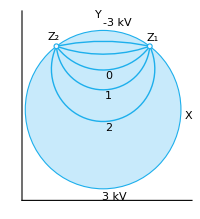

```mathematica
topgraphics=Graphics[{{EdgeForm[Directive[Thick,outerb]],innerb,Disk[{0,0},1]},{},{Point[{0.6,0.8}]},{Point[{-0.6,0.8}]},{},{outerb,Circle[{0,0.8522},0.6022,{-(3π)/4+-0.68,π/7-0.53}]},{outerb,Circle[{0,0.5144},0.6644,{-π+-0.45,π/7}]},{outerb,Circle[{0,1.25},0.75,{-π/2+-0.91,π/50-0.7}]},{outerb,Circle[{0,2.55},1.85,{-π/2+-0.325,-π/3-0.2}]},{outerb,Circle[{0,-2.068},2.931,{π/2-0.2,π/2+0.2}]},{EdgeForm[Directive[outerb]],innerbw,Disk[{0.6,0.8},0.03]},{EdgeForm[Directive[outerb]],innerbw,Disk[{-0.6,0.8},0.03]},{Text[Style[1,Medium],{0.07,0.169}]},{Text[Style[0,Medium],{0.07,0.42}]},{Text[Style[2,Medium],{0.07,-0.23}]},{Text[Style[3 kV,Medium],{0.15,-1.1}]},{Text[Style[-3 kV,Medium],{0.185,1.1}]},{Text[Style[Y,Medium],{-0.06,1.2}]},{Text[Style["Z_1",Medium],{0.64,0.9}]},{Text[Style["Z_2",Medium],{-0.64,0.92}]},{Text[Style[X,Medium],{1.1,-0.08}]}},Axes->True,Ticks->None,AxesStyle->Medium,ImageSize->200]
```

LFT (linear fractional transformation) tends to signify the 3-point transfer task, but it is more than that. For mapping a circle onto another circle, the numbered line (3) on p. 749 is the one that tells how. It looks like

```mathematica
w[z_]=(z-Subscript[z, 0])/(c z-1)
```

(z-z_0)/(-1+c z)

and the requirements for z_0 and c are that z_0 is the point destined to map to the new circle’s center, and c is the conjugate of z_0. (Also, Abs[z_0] < 1.)  So in the present case

```mathematica
w1[z_]=w[z]/.{Subscript[z, 0]->ⅈ/2,c->ⅈ/2*}
```

(-ⅈ/2+z)/(-1-(ⅈ z)/2)

or

```mathematica
w2[z_]=(2z-ⅈ)/(-2-ⅈ z)
```

(-ⅈ+2 z)/(-2-ⅈ z)

The cell above matches the answer in the text.

```mathematica
w3[{x_,y_}]=(-ⅈ+2 z)/(-2-ⅈ z)/.z->(x+ⅈ y)
```

(-ⅈ+2 (x+ⅈ y))/(-2-ⅈ (x+ⅈ y))

```mathematica
Chop[w3[{0.6,0.8}]]
```

-1.

```mathematica
Chop[w3[{-0.6,0.8}]]
```

1.

Pertaining to Chop, it uses a default tolerance of 10^-10, here chopping a tiny wisp of imaginary.

```mathematica
w3[{0,1/2}]
```

0

I build some data to record the changes involved in the transformation.

```mathematica
so={{0,1/2},{0.6,0.8},{-0.6,0.8},{0,1},{0,2},{0,-1},{0,-2}}
```

{{0,1/2},{0.6,0.8},{-0.6,0.8},{0,1},{0,2},{0,-1},{0,-2}}

```mathematica
Thread[w3[ so]]
```

Power::infy: Infinite expression 1/0 encountered.

{0,-1.-5.55112×10^-17 ⅈ,1.-5.55112×10^-17 ⅈ,-ⅈ,ComplexInfinity,ⅈ,(5 ⅈ)/4}

```mathematica
botgraphics=Graphics[{{Circle[{0,0},1,{0,2π}]},{Red,PointSize[0.025],Point[{0,0}]},{Green,PointSize[0.025],Point[{1,0}]},{Blue,PointSize[0.025],Point[{-1,0}]},{Brown,PointSize[0.025],Point[{0,1}]},{Black,PointSize[0.025],Point[{0,-1}]}},Axes->True,ImageSize->200];
```

```mathematica
data={{"0",{0,1/2},{0,0}},{"Z_1",{0.6,0.8},{-1,0}},{"Z_2",{-0.6,0.8},{1,0}},{"-3kV",{0,1},{0,-1}},{"3 kV",{0,-1},{0,1}}};
```

```mathematica
textbox=Text@Grid[Prepend[data,{"Old Label","Old Point","New Point"}],Frame->All,Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}}];
```

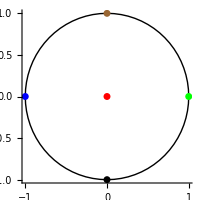
-Graphics--Graphics-Old Label | Old Point | New Point
0 | {0,1/2} | {0,0}
Z_1 | {0.6,0.8} | {-1,0}
Z_2 | {-0.6,0.8} | {1,0}
-3kV | {0,1} | {0,-1}
3 kV | {0,-1} | {0,1}

```mathematica
Row[{topgraphics,botgraphics,textbox}]
```

A glance at the cell above shows the flips and changes due to the current transformation.

19.  Jump on the boundary. Find the complex and real potentials in the upper half-plane with boundary values 5 kV if x < 2 and 0 if x > 2 on the x-axis.

```mathematica
Clear["Global`*"]
```

```mathematica
d2=ImplicitRegion[-∞<x<∞∧0<y<∞,{x,y}];
```

```mathematica
grap=RGBColor[0.529,0.474,0.694];
```

```mathematica
ParametricPlot[Through[{Re,Im}[x+ⅈ y]],{x,y}∈d2, PlotRange->{{-1,3.5},{-3,3}},Frame->True,ImageSize->200,AspectRatio->Automatic,Epilog->{{grap,Dashed,Thick,Line[{{2,-10},{2,10}}]},{Text[Style["U_1=5",Medium],{1.5,-0.15}]},{Text[Style["U_2=0",Medium],{2.5,-0.15}]}}]
```

-Graphics-

Judging from the text answer, this problem can be modeled against example 3 on p. 760. Physically, I can imagine two plates being rotated apart until the angle of separation is π. The combined potential Φ is calculated according to one of two formulas.

```mathematica
Φ[x_,y_]=a + b Arg[z]
```

a+b Arg[z]

```mathematica
Solve[a+b(-1/2 π)==0&&a+b(1/2 π)==5,{a,b}]
```

{{a→5/2,b→5/π}}

```mathematica
Φ[x_,y_]=a + b Arg[z]/.{a->5/2,b->5/π}
```

5/2+(5 Arg[z])/π

The text does two things which make the above cell unequal to the text answer. First thing is to ignore, cancel, or eliminate the a factor. The second thing, which is not discussed in example 3, is to compensate the z value for the separation of the fulcrum point from x=0.  That is, the text answer is

```mathematica
(5 Arg[z-2])/π
```

Which seems like a very good answer, and I don’t doubt there is some reason the a drops out. Going on to the determination of F, example 6 on p. 761 takes care of that with a simple formula.

```mathematica
eFF[z_]=a - ⅈ b Log[z]
```

a-ⅈ b Log[z]

If I stick with the non-zero a, I would have to build it as

```mathematica
5/2-(5 ⅈ)/π Log[z-2]
```

However, having dispensed with the a=5/2, the text answer stays rid of it and reports the remainder as F.